```mathematica
K=Integrate[x[θ,c+r],{θ,a,b[r]}]
```

∫_a^b[r] x[θ,c+r]ⅆθ

```mathematica
D[K,r]
```

∫_a^b[r] x^(0,1)[θ,c+r]ⅆθ+x[b[r],c+r] b'[r]

```mathematica
Integrate[u'[x[θ,r]]/u''[x[θ,r]],{θ,a,b}]
```

```mathematica
D[∫_a^b u'[x[θ,r]]/u''[x[θ,r]] ⅆθ,r]//FullSimplify
```

∫_a^b (1-(u'[x[θ,r]] u^(3)[x[θ,r]])/u''[x[θ,r]]^2) x^(0,1)[θ,r]ⅆθ

```mathematica
Integrate[θ*x'[θ],θ]
```

∫θ x'[θ]ⅆθ

```mathematica
DSolve[k'[r]==(1/(c+r))*(z - k[r]),k[r],r]
```

{{k[r]→(r z)/(c+r)+C[1]/(c+r)}}

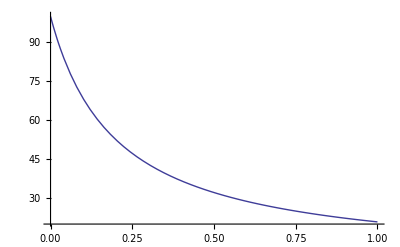

```mathematica
Plot[(r z)/(c+r)+(d0*c)/(c+r)/.{c->.2,d0->100,z->5},{r,0,1}]
```

```mathematica
D[(r z)/(c+r)+(d0*c)/(c+r),r]/((r z)/(c+r)+(d0*c)/(c+r))//FullSimplify
```

(c (-d0+z))/((c+r) (c d0+r z))

## Uniform Case

```mathematica
u[x_]:=Log[x+1];
sol = Solve[D[θ*u[x] - (c+r)*x,x]==0,x]
```

{{x→(-c-r+θ)/(c+r)}}

```mathematica
x[θ_,r_]=x/.sol[[1]]
```

(-c-r+θ)/(c+r)

```mathematica
A higher rental rate reduces usage.
```

```mathematica
D[x[θ,r],r]//FullSimplify
```

-θ/(c+r)^2

```mathematica
v[θ,r] := θ*u[x[θ,r]]-(c+r)*x[θ,r]
```

```mathematica
v[θ,r]//FullSimplify
```

c+r-θ+θ Log[θ/(c+r)]

```mathematica
The first users to participate has θ = c + r.
```

```mathematica
v[θ,r]/.{θ->c+r}
```

0

```mathematica
For everyone that rents, indirect utility is decreasing in the rental rate.
```

```mathematica
D[v[θ,r],r]//FullSimplify
```

1-θ/(c+r)

## Who buys?

```mathematica
θ*u[x[θ,0]] - c*x[θ,0]==p//FullSimplify
```

```mathematica
Solve[c+θ Log[θ/c]==p+θ,θ]
```

{{θ→(-c+p)/ProductLog[(-c+p)/(c ⅇ)]}}

```mathematica
Series[(-c+p)/ProductLog[(-c+p)/(c ⅇ)],{p,0,4}]
```

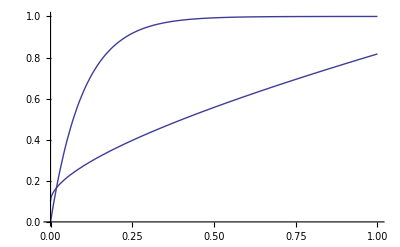

```mathematica
Plot[{1-Exp[(-1/c)*p],(-c+p)/ProductLog[(-c+p)/(c ⅇ)]}/.c->0.1,{p,0,1}]
```

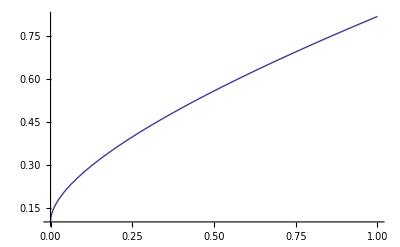

```mathematica
Plot[(-c+p)/ProductLog[(-c+p)/(c ⅇ)]/.{c->0.1},{p,0,1}]
```

```mathematica
D[(-c+p)/ProductLog[(-c+p)/(c ⅇ)],p]/((-c+p)/ProductLog[(-c+p)/(c ⅇ)])//FullSimplify
```

```mathematica
Limit[(-1+1/(1+ProductLog[(-c+p)/(c ⅇ)]))/(c-p),c->0]
```

1/p

```mathematica
Clear[θBM]
```

```mathematica
Solve[(1-x[θ,r])*r ==γ,θ]
```

{{θ→((c+r) (2 r-γ))/r}}

```mathematica
Integrate[(1-x[θ,r]),{θ,(-c+p)/ProductLog[(-c+p)/(c ⅇ)],((c+r) (2 r-γ))/r}]//FullSimplify
```

```mathematica
S[r_]:=1/2 (-4 c ⅇ^(1+ProductLog[(-c+p)/(c ⅇ)])+(c^2 ⅇ^(2 (1+ProductLog[(-c+p)/(c ⅇ)])))/(c+r)+(c+r) (4-γ^2/r^2))
```

```mathematica
D[S[r],γ]//FullSimplify
```

-((c+r) γ)/r^2

```mathematica
D[S[r],r]//FullSimplify
```

```mathematica
1/2 (4-(c^2 ⅇ^(2 (1+ProductLog[(-c+p)/(c ⅇ)])))/(c+r)^2+((2 c+r) γ^2)/r^3)
```

```mathematica
Solve[Integrate[x[θ,r],{θ,c+r,θB}]==Integrate[1-x[θ,r],{θ,θB,θM}],r]//FullSimplify
```

{{r→-c-θB-√((θB-3 θM) (θB-θM))+2 θM},{r→-c-θB+√((θB-3 θM) (θB-θM))+2 θM}}

```mathematica
trainingSet = {1->1.2, 2->2.4, 3->6.4, 3->10}
```

{1→1.2,2→2.4,3→6.4,3→10}

```mathematica
Predict[trainingSet]
```

Predict[{1→1.2,2→2.4,3→6.4,3→10}]

```mathematica
Integrate[-θ/(p + c*x),p]
```

-θ Log[p+c x]

```mathematica
D[1 - θ[p]/(p + c*x[p]),p]//FullSimplify
```

(θ[p] (1+c x'[p])-(p+c x[p]) θ'[p])/(p+c x[p])^2

```mathematica
Integrate[θB/(1+p*x[θB]),θB]
```

∫θB/(1+p x[θB])ⅆθB

```mathematica
D[1/(1+p x[θB]),θB]
```

-(p x'[θB])/(1+p x[θB])^2